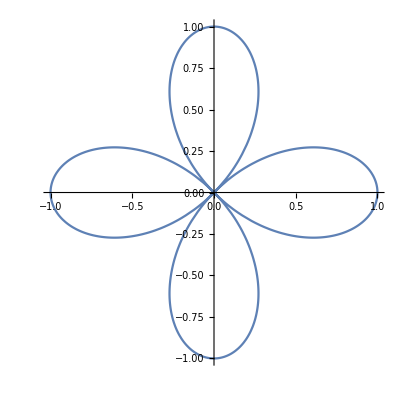

```mathematica
(* Rosa de cuatro pétalos *)
ParametricPlot[{Cos[2*u]*Cos[u],Cos[2*u]*Sin[u]},{u,0,2 Pi}]
```

```mathematica
(* Cilindro de la rosa de cuatro pétalos *)
ParametricPlot3D[{Cos[2 u] Cos[u],Cos[2 u] Sin[u],v},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Cono de la rosa de cuatro pétalos *)
ParametricPlot3D[{v*Cos[2 u] * Cos[u],v*Cos[2 u] * Sin[u], v},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

```mathematica
-Graphics3D-
(* Conoide de Wallis con a=b=c=1 *)
ParametricPlot3D[{v*Cos[u],v*Sin[u], Sqrt[1-Cos[u]^2]},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

```mathematica
-Graphics3D-
(* Conoide de Plücker con n=2 *)
ParametricPlot3D[{v*Cos[u],v*Sin[u], Sin[2*u]},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-

```mathematica
(* Conoide de Plücker generalizado *)
n = 3;
ParametricPlot3D[{v*Cos[u],v*Sin[u], Sin[n*u]},{u,0,2 π},{v,0,1},PlotStyle->RGBColor[0.17,0.47000000000000003,1.],PlotTheme->"Business"]
```

-Graphics3D-